```mathematica
β = 1;
n = 10;
Jnn = 1;
Jnnn = 1;
d = 6*Max[{Abs[Jnn], Abs[Jnnn]}];
```

Generating matrices

```mathematica
NN = DiagonalMatrix[Array[1&,n-1],1] + DiagonalMatrix[Array[1&,n-1],-1];
NN[[n,1]] = 1;
NN[[1,n]] = 1;

NNN = DiagonalMatrix[Array[1&,n-2],2] + DiagonalMatrix[Array[1&,n-2],-2];
NNN[[n-1,1]] = 1;
NNN[[n,2]] = 1;
NNN[[1,n-1]] = 1;
NNN[[2,n]] = 1;

J = β * (Jnn*NN + Jnnn*NNN);
K = β * (Jnn*NN + Jnnn*NNN+ d*DiagonalMatrix[Array[1&,n],0]);
H = β * (Array[1&,n]);
```

```mathematica
ϕ = Array[x , n] // MatrixForm
Exp[-0.5*ϕᵀ.K.ϕ] * Product[Cosh[H[[i]] + phiᵀ.K[[i]]], {i,1,n}]
```

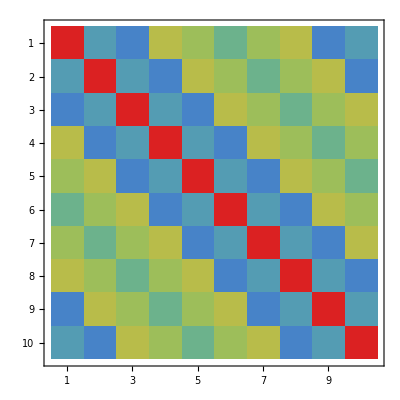

```mathematica
Inverse[K] // MatrixForm;
MatrixPlot[Inverse[K],ColorFunction->"Rainbow",PlotLegends->BarLegend[Automatic,LegendFunction->"Frame"]]
```

```mathematica
K
```

{{22,-3,-3,2,-3,-3},{-3,22,-3,-3,2,-3},{-3,-3,22,-3,-3,2},{2,-3,-3,22,-3,-3},{-3,2,-3,-3,22,-3},{-3,-3,2,-3,-3,22}}

```mathematica
K // MatrixForm
```

(6 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 6 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 6 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 6 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 6 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 6 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 6 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 6 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 6 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 6)